# Time Constant Calculator from Simulation Data

## Setup (automatically initialized when this notebook is opened)

```mathematica
$HistoryLength=10;
```

### Function definitions

#### OrganizeWFData[fileName_,timeBounds_]

This function takes the filename of a waveform and extracts the coordinates of the waveform plot.  It also takes the timeBounds variable as input.  timeBounds is a variable that defines the start and stop times between which the data should be taken.

As output, this function returns a single data member which is organized as {axesLabel, d, numTaus}.

```mathematica
OrganizeWFDataMultTau[fileName_]:=Module[{axesLabel,d,numTaus,i},
i=Import[fileName,"Data"];
axesLabel=i⟦1⟧;
d=i⟦2;;⟧;
numTaus=Length[i⟦1⟧]-1;
Clear[i];
Return[{axesLabel,d,numTaus}];
](* OrganizeWFDataMultTau Module *)
```

#### DataToPlotFormat[data_]

This function takes a data file and organizes it such that for each Ilk value, there is an independent xValue column corresponding to the yValue column

As output, this function returns a single data member which is organized as a list of sublists.  Each sublist corresponds to a different τ value and is comprised by a list of x,y coordinates that can be used to plot the data.

```mathematica
DataToPlotFormat[data_]:=Module[{organizedData},
organizedData=Transpose[data];
organizedData=Select[Transpose[{organizedData⟦1⟧,#}],NumberQ[#⟦2⟧]&]&/@organizedData⟦2;;⟧;
Return[organizedData];
](* DataToPlotFormat Module *)
```

### Ask user to select an input file with the waveform data

This section opens a system dialog box that asks the user to select a waveform file with the waveform trace.  It then sets the default working directory equal to the directory where this file is located.

```mathematica
fileName=SystemDialogInput["FileOpen","/home/noza/work/Mathematica/Scripts/LPFTimeConstantMeasurements", WindowTitle->"Select Simulation Waveform File (*.txt)"];
workingDir=DirectoryName[fileName];
SetDirectory[workingDir];
Print[Style["Working Directory:  ",FontFamily->"Helvetica", Bold] ,Style[Directory[],Italic]];
Print[Style["File Name: ", FontFamily->"Helvetica", Bold],FileNameTake[fileName]];
iInVal=ToExpression[Flatten[StringCases[fileName,"LPFWaveform_iin_"~~iIn:NumberString~~"_tau_sweep.txt"->iIn]]];
```

Working Directory:  /home/noza/work/Mathematica/Scripts/LPFTimeConstantMeasurements

File Name: LPFWaveform_iin_0.50_tau_sweep.txt

## Information Processing (Run-time) - Falling Edge

### Process Waveform Data from Input File

This section takes the fileName gotten from the selection dialog and imports the data using the OrganizeWFData function defined in the functions section.  It then filters that data to the selected region, where the selected region specifies the data points that fit an exponential decay model.

```mathematica
timeBounds ={0.5001,1.5};
AbsoluteTiming[{axesLabel,data,numTaus}=OrganizeWFDataMultTau[fileName]];(*Import data*)
(* Filter out data to get just the decay portion of the curve *)
timeFilteredData=Select[data,#⟦1⟧>timeBounds⟦1⟧&];
timeFilteredData=Select[timeFilteredData,#⟦1⟧<=timeBounds⟦2⟧&];
timeFilteredData=DataToPlotFormat[timeFilteredData];(*Organize data to allow it to be plottable*)
d=DataToPlotFormat[data];(*Organize data to allow it to be plottable*)
(* Extract tau values and labels from imported dataset *)
tauLabels=Rest[axesLabel];
tauVals=ToExpression[Flatten[StringCases[tauLabels,"i(vmeas_im):tau_"~~tau:NumberString~~"`"-> tau]]];
(* Take only positive current values as valid data *)
validTimeFilteredData=Select[#,#⟦2⟧>0&]&/@timeFilteredData;
(*Get important values for fitting a linear fit*)
Isats=Max[#⟦;;,2⟧]&/@validTimeFilteredData;
offsetMins=Min[#⟦;;,2⟧]-10^-17&/@validTimeFilteredData;
(* Clear timeFilteredData from memory *)
Clear[timeFilteredData, data,tauLabels];
```

### Plot Data

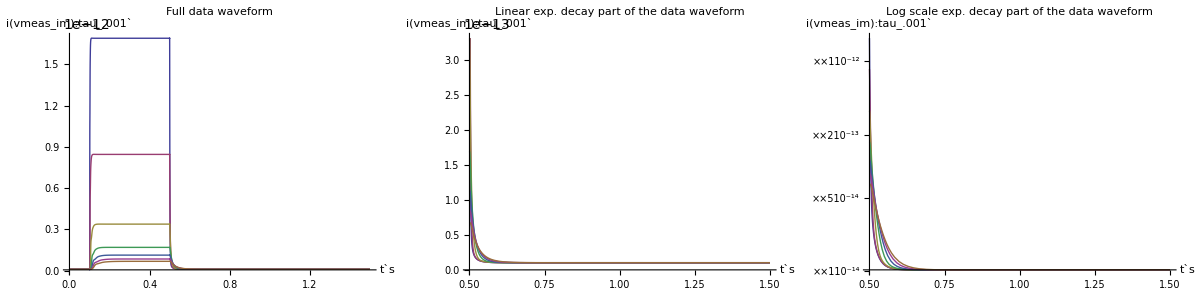
Data Waveforms
-Graphics-

```mathematica
imgSize=350;
Grid[{
{Text[Style["Data Waveforms",Bold,18]]},
{Grid[{
{ListLinePlot[d,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All}],
ListLinePlot[validTimeFilteredData,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Linear exp. decay part of the data waveform",Bold]],
ListLogPlot[validTimeFilteredData,AxesLabel->axesLabel,Joined->True,ImageSize->imgSize, PlotLabel->Style["Log scale exp. decay part of the data waveform",Bold]]}
}]}
}]
```

### Manipulate Data

#### Calculate τ using linear fit manually accounting for offset

```mathematica
imgSize=500;
defaultPlotNum=1;
workPrec=Automatic;
offsetLessData=validTimeFilteredData⟦defaultPlotNum⟧-offsetMins⟦defaultPlotNum⟧;
(* Extract x-values from dataset *)
xVals=Transpose[offsetLessData]⟦1⟧;
xValsExp=Transpose[validTimeFilteredData⟦defaultPlotNum⟧]⟦1⟧;
TabView[{
"Linear Log Fit"->
Manipulate[
plotNum=Sequence@@Flatten[Position[tauVals,plotID]];
offsetLessData=validTimeFilteredData⟦plotNum⟧-offsetMins⟦plotNum⟧;
xVals=Transpose[offsetLessData]⟦1⟧;
(* Select exponential range of data *)
boundedOffsetLessData=Select[offsetLessData,#⟦1⟧>=lowerBound&];
boundedOffsetLessData=Select[boundedOffsetLessData,#⟦1⟧<=upperBound&];
(* Shift the data so that the exponential curve is shifted left, such that the curve crosses the y-axis at the correct Isat value *)
shiftedBoundedOffsetLessData=Transpose[{boundedOffsetLessData⟦;;,1⟧-lowerBound,boundedOffsetLessData⟦;;,2⟧}];
logOffsetLessData=Transpose[{shiftedBoundedOffsetLessData⟦;;,1⟧,Log[shiftedBoundedOffsetLessData⟦;;,2⟧]}];
(* Find the best fit *)
fitLineEq=Fit[logOffsetLessData,{1,t},t];
fitLineRules=FindFit[logOffsetLessData,m t+b,{{m,-1/tauVals⟦plotNum⟧},b},t];
τ=-1/m/.fitLineRules;
errTau=Abs[τ-tauVals⟦plotNum⟧];percErrTau=(errTau/tauVals⟦plotNum⟧)*100;
(*A little memory management*)
Clear[boundedOffsetLessData, offsetLessData];
Grid[{
{Row[{Style["ι_in:  ",FontFamily->"Helvetica", Bold] ,Style[iInVal,Italic]}],
Row[{Style["File Name:  ",FontFamily->"Helvetica", Bold] ,Style[FileNameTake[fileName],Italic]}]},
{Row[{Style["Measured Isat:  ",FontFamily->"Helvetica", Bold] ,Style[Isats⟦plotNum⟧,Italic]}],
Row[{Style["Extracted Isat:  ",FontFamily->"Helvetica", Bold] ,Style[ⅇ^b/.fitLineRules,Italic]}]},
{Row[{Style["Measured offset:  ",FontFamily->"Helvetica", Bold] ,Style[offsetMins⟦plotNum⟧,Italic]}],
Row[{Style["Fit Equation:  ",FontFamily->"Helvetica", Bold] ,Style[fitLineEq,Italic]}]},
{Show[(*ListPlot[logSelData,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Red],*)
ListLogPlot[shiftedBoundedOffsetLessData,AxesLabel->axesLabel,ImageSize->imgSize,PlotRange->{{0,upperBound-lowerBound},{0,All}},PlotStyle->Red],
Plot[fitLineEq,{t,0,upperBound-lowerBound}]
],
Grid[{
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[τ,Italic]}]},
{Row[{Style["Δτ:  ",FontFamily->"Helvetica", Bold] ,Style[errTau,Italic]}]},
{Row[{Style["τ_err(%):  ",FontFamily->"Helvetica", Bold] ,Style[percErrTau,Italic]}]}
}]}
}],
{{plotID,tauVals⟦defaultPlotNum⟧,"Theoretical τ Value"},tauVals},
{{lowerBound,xVals⟦10⟧,"Lower Bound"},Dynamic[Take[xVals,Ceiling[Length[xVals]*3/4]]],Appearance->{"Labeled","Open"}},
{{upperBound,xVals⟦Floor[Length[Most[xVals]]/3]⟧,"Upper Bound"},Dynamic[Most[xVals]],Appearance->{"Labeled","Open"}},
LabelStyle->Medium,
UnsavedVariables->{fitLineEq,fitLineRules,errTau,logOffsetLessData,shiftedBoundedOffsetLessData,τ,xVals,plotNum},
TrackedSymbols->{plotID,lowerBound,upperBound}
](*Manipulate Linear *)
},1](*TabView *)
```

1

### Data Analysis

#### Accuracy of Tau Values as measured from the exponential fit manipulator

This table will hold the data obtained manually from playing with the manipulator to find the minimum percentage error in tau.

```mathematica
percErrTauRawDataExp=({{0, .001, .002, .005, .010, .015, .020, .025}, {0.25, 0.2781, .2892, .2856, .288, .2593, .198, .1511}, {0.5, .0055, .0036, .0162, .0023, .0021, .0022, .0012}, {0.75, .0005, .0037, .0002, .0002, .00003, .0026, .0044}, {1.00, .0007, .0001, .0021, .00003, .0017, .0032, .0031}, {1.25, .0021, .0008, .0006, .0002, .0012, .0002, .0012}, {3, .0001, .0020, .0008, .00005, .0004, .0011, .0004}});
percErrTauValsExp=Rest[percErrTauRawDataExp⟦1⟧];
percErriinValsExp=Rest[Transpose[percErrTauRawDataExp]⟦1⟧];
percErrPlotValsExp=Transpose[Rest[Transpose[Rest[percErrTauRawDataExp]]]];
MatrixPlot[percErrPlotValsExp,PlotRange->{Min[percErrPlotValsExp],Max[percErrPlotValsExp]},ColorFunctionScaling->True,ColorFunction->"CherryTones",PlotLabel->"Percentage Error of τ",AxesLabel->{"Expected τ value","ι_in value"},PlotLegends->True]
```

-Graphics-

#### Accuracy of Tau Values as measured from the linear fit manipulator

This table will hold the data obtained manually from playing with the manipulator to find the minimum percentage error in tau.

```mathematica
percErrTauRawData=({{0, .001, .002, .005, .010, .015, .020, .025}, {0.25, 0.4270, 0.4105, 0.3824, 0.3208, 0.2499, 0.1815, 0.1276}, {0.5, 0.0672, 0.0546, 0.0473, 0.0336, 0.0172, 0.0105, 0.0005}, {0.75, 0.0049, 0.0013, 0.0002, 0.0018, 0.0013, 0.0007, 0.0006}, {1.00, 0.0014, 0.0011, 0.0025, 0.0015, 0.0023, 0.0019, 0.0008}, {1.25, 0.0004, 0.0039, 0.0010, 0.0022, 0.0018, 0.0027, 0.0003}, {3, 0.0039, 0.0047, 0.0018, 0.0025, 0.0036, 0.0026, 0.0025}});
percErrTauVals=Rest[percErrTauRawData⟦1⟧];
percErriinVals=Rest[Transpose[percErrTauRawData]⟦1⟧];
percErrPlotVals=Transpose[Rest[Transpose[Rest[percErrTauRawData]]]];
MatrixPlot[percErrPlotVals,PlotRange->{Min[percErrPlotVals],Max[percErrPlotVals]},ColorFunctionScaling->True,ColorFunction->"CherryTones",PlotLabel->"Percentage Error of τ",AxesLabel->{"Expected τ value","ι_in value"},PlotLegends->True]
```

-Graphics-

## Information Processing (Run-time) - Rising Edge

### Process Waveform Data from Input File

This section takes the fileName gotten from the selection dialog and imports the data using the OrganizeWFData function defined in the functions section.  It then filters that data to the selected region, where the selected region specifies the data points that fit an exponential decay model.

```mathematica
timeBoundsRE ={0.1,0.4};
AbsoluteTiming[{axesLabelRE,dataRE,numTausRE}=OrganizeWFDataMultTau[fileName]];(*Import data*)
(* Filter out data to get just the decay portion of the curve *)
timeFilteredDataRE=Select[dataRE,#⟦1⟧>timeBoundsRE⟦1⟧&];
timeFilteredDataRE=Select[timeFilteredDataRE,#⟦1⟧<=timeBoundsRE⟦2⟧&];
timeFilteredDataRE=DataToPlotFormat[timeFilteredDataRE];(*Organize data to allow it to be plottable*)
dRE=DataToPlotFormat[dataRE];(*Organize data to allow it to be plottable*)
(* Extract tau values and labels from imported dataset *)
tauLabelsRE=Rest[axesLabelRE];
tauValsRE=ToExpression[Flatten[StringCases[tauLabelsRE,"i(vmeas_im):tau_"~~tauRE:NumberString~~"`"-> tauRE]]];
(* Take only positive current values as valid data *)
validTimeFilteredDataRE=Select[#,#⟦2⟧>0&]&/@timeFilteredDataRE;
(*Get important values for fitting a linear fit*)
IsatsRE=Max[#⟦;;,2⟧]&/@validTimeFilteredDataRE;
offsetMinsRE=Min[#⟦;;,2⟧]-10^-17&/@validTimeFilteredDataRE;
(* Clear timeFilteredData from memory *)
Clear[timeFilteredData, data,tauLabels];
```

### Plot Data

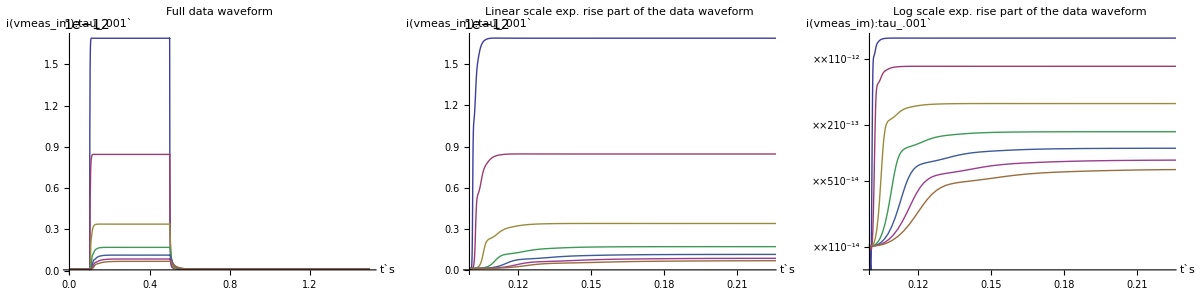
Data Waveforms
-Graphics-

```mathematica
imgSizeRE=350;
Grid[{
{Text[Style["Data Waveforms",Bold,18]]},
{Grid[{
{ListLinePlot[dRE,AxesLabel->axesLabel,ImageSize->imgSizeRE, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All}],
ListLinePlot[validTimeFilteredDataRE,AxesLabel->axesLabelRE,ImageSize->imgSizeRE, PlotLabel->Style["Linear scale exp. rise part of the data waveform",Bold]],
ListLogPlot[validTimeFilteredDataRE,AxesLabel->axesLabelRE,Joined->True,ImageSize->imgSizeRE, PlotLabel->Style["Log scale exp. rise part of the data waveform",Bold]]}
}]}
}]
```

### Manipulate Data (ToDo)

#### Calculate τ using linear fit manually accounting for offset

```mathematica
imgSizeRE=500;
defaultPlotNumRE=1;
workPrecRE=Automatic;
offsetLessDataRE=validTimeFilteredDataRE⟦defaultPlotNumRE⟧-offsetMinsRE⟦defaultPlotNumRE⟧;
(* Extract x-values from dataset *)
xValsRE=Transpose[offsetLessDataRE]⟦1⟧;
xValsExpRE=Transpose[validTimeFilteredDataRE⟦defaultPlotNumRE⟧]⟦1⟧;
TabView[{
"Linear Log Fit"->
Manipulate[
plotNumRE=Sequence@@Flatten[Position[tauValsRE,plotIDRE]];
offsetLessDataRE=validTimeFilteredDataRE⟦plotNumRE⟧-offsetMinsRE⟦plotNumRE⟧;
xValsRE=Transpose[offsetLessDataRE]⟦1⟧;
(* Select exponential range of data *)
boundedOffsetLessDataRE=Select[offsetLessDataRE,#⟦1⟧>=lowerBoundRE&];
boundedOffsetLessDataRE=Select[boundedOffsetLessDataRE,#⟦1⟧<=upperBoundRE&];
(* Shift the data so that the exponential curve is shifted left, such that the curve crosses the y-axis at the correct Isat value *)
shiftedBoundedOffsetLessDataRE=Transpose[{boundedOffsetLessDataRE⟦;;,1⟧-lowerBoundRE,boundedOffsetLessDataRE⟦;;,2⟧}];
logOffsetLessDataRE=Transpose[{shiftedBoundedOffsetLessDataRE⟦;;,1⟧,Log[shiftedBoundedOffsetLessDataRE⟦;;,2⟧]}];
(* Find the best fit *)
fitLineEqRE=Fit[logOffsetLessDataRE,{1,t},t];
fitLineRulesRE=FindFit[logOffsetLessDataRE,m t+b,{{m,-1/tauValsRE⟦plotNumRE⟧},b},t];
τRE=-1/m/.fitLineRulesRE;
errTauRE=Abs[τRE-tauValsRE⟦plotNumRE⟧];percErrTauRE=(errTauRE/tauValsRE⟦plotNumRE⟧)*100;
(*A little memory management*)
Clear[boundedOffsetLessDataRE, offsetLessDataRE];
Grid[{
{Row[{Style["ι_in:  ",FontFamily->"Helvetica", Bold] ,Style[iInVal,Italic]}],
Row[{Style["File Name:  ",FontFamily->"Helvetica", Bold] ,Style[FileNameTake[fileName],Italic]}]},
{Row[{Style["Measured Isat:  ",FontFamily->"Helvetica", Bold] ,Style[IsatsRE⟦plotNumRE⟧,Italic]}],
Row[{Style["Extracted Isat:  ",FontFamily->"Helvetica", Bold] ,Style[ⅇ^b/.fitLineRulesRE,Italic]}]},
{Row[{Style["Measured offset:  ",FontFamily->"Helvetica", Bold] ,Style[offsetMinsRE⟦plotNumRE⟧,Italic]}]},
{Show[(*ListPlot[logSelData,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Red],*)
ListLogPlot[shiftedBoundedOffsetLessDataRE,AxesLabel->axesLabelRE,ImageSize->imgSizeRE,PlotRange->{{0,upperBoundRE-lowerBoundRE},{0,All}},PlotStyle->Red],
Plot[fitLineEqRE,{t,0,upperBoundRE-lowerBoundRE}]
],
Grid[{
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[τRE,Italic]}]},
{Row[{Style["Δτ:  ",FontFamily->"Helvetica", Bold] ,Style[errTauRE,Italic]}]},
{Row[{Style["τ_err(%):  ",FontFamily->"Helvetica", Bold] ,Style[percErrTauRE,Italic]}]}
}]}
}],
{{plotIDRE,tauValsRE⟦defaultPlotNumRE⟧,"Theoretical τ Value"},tauValsRE},
{{lowerBoundRE,xValsRE⟦10⟧,"Lower Bound"},Dynamic[Take[xValsRE,Ceiling[Length[xValsRE]*3/4]]],Appearance->{"Labeled","Open"}},
{{upperBoundRE,xValsRE⟦Floor[Length[Most[xValsRE]]/3]⟧,"Upper Bound"},Dynamic[Most[xValsRE]],Appearance->{"Labeled","Open"}},
LabelStyle->Medium,
UnsavedVariables->{fitLineEqRE,fitLineRulesRE,errTauRE,logOffsetLessDataRE,shiftedBoundedOffsetLessDataRE,τRE,xValsRE,plotNumRE},
TrackedSymbols->{plotIDRE,lowerBoundRE,upperBoundRE}
](*Manipulate Linear *)
},1](*TabView *)
```

1

### Data Analysis

#### Accuracy of Tau Values as measured from the exponential fit manipulator

This table will hold the data obtained manually from playing with the manipulator to find the minimum percentage error in tau.

```mathematica
percErrTauRawDataExp=({{0, .001, .002, .005, .010, .015, .020, .025}, {0.25, 0.2781, .2892, .2856, .288, .2593, .198, .1511}, {0.5, .0055, .0036, .0162, .0023, .0021, .0022, .0012}, {0.75, .0005, .0037, .0002, .0002, .00003, .0026, .0044}, {1.00, .0007, .0001, .0021, .00003, .0017, .0032, .0031}, {1.25, .0021, .0008, .0006, .0002, .0012, .0002, .0012}, {3, .0001, .0020, .0008, .00005, .0004, .0011, .0004}});
percErrTauValsExp=Rest[percErrTauRawDataExp⟦1⟧];
percErriinValsExp=Rest[Transpose[percErrTauRawDataExp]⟦1⟧];
percErrPlotValsExp=Transpose[Rest[Transpose[Rest[percErrTauRawDataExp]]]];
MatrixPlot[percErrPlotValsExp,PlotRange->{Min[percErrPlotValsExp],Max[percErrPlotValsExp]},ColorFunctionScaling->True,ColorFunction->"CherryTones",PlotLabel->"Percentage Error of τ",AxesLabel->{"Expected τ value","ι_in value"},PlotLegends->True]
```

-Graphics-

#### Accuracy of Tau Values as measured from the linear fit manipulator

This table will hold the data obtained manually from playing with the manipulator to find the minimum percentage error in tau.

```mathematica
percErrTauRawData=({{0, .001, .002, .005, .010, .015, .020, .025}, {0.25, 0.4270, 0.4105, 0.3824, 0.3208, 0.2499, 0.1815, 0.1276}, {0.5, 0.0672, 0.0546, 0.0473, 0.0336, 0.0172, 0.0105, 0.0005}, {0.75, 0.0049, 0.0013, 0.0002, 0.0018, 0.0013, 0.0007, 0.0006}, {1.00, 0.0014, 0.0011, 0.0025, 0.0015, 0.0023, 0.0019, 0.0008}, {1.25, 0.0004, 0.0039, 0.0010, 0.0022, 0.0018, 0.0027, 0.0003}, {3, 0.0039, 0.0047, 0.0018, 0.0025, 0.0036, 0.0026, 0.0025}});
percErrTauVals=Rest[percErrTauRawData⟦1⟧];
percErriinVals=Rest[Transpose[percErrTauRawData]⟦1⟧];
percErrPlotVals=Transpose[Rest[Transpose[Rest[percErrTauRawData]]]];
MatrixPlot[percErrPlotVals,PlotRange->{Min[percErrPlotVals],Max[percErrPlotVals]},ColorFunctionScaling->True,ColorFunction->"CherryTones",PlotLabel->"Percentage Error of τ",AxesLabel->{"Expected τ value","ι_in value"},PlotLegends->True]
```

-Graphics-

## Appendix

### Calculate τ using exponential fit automatically accounting for offset

If anyone wants the legacy code used to perform exponential fits automatically, they can copy the commented code below and put it into the tab-view manipulator above in the Manipulate Data section.  That will allow them to play with both types of extraction models (linear log or exponential)

```mathematica
(*"Exponential Fit"->
Manipulate[
plotNumExp=Sequence@@Flatten[Position[tauVals,plotIDExp]];
xValsExp=Transpose[validTimeFilteredData⟦plotNumExp⟧]⟦1⟧;
(* Select exponential range of data *)
selDataExp=Select[validTimeFilteredData⟦plotNumExp⟧,#⟦1⟧>=lowerBoundExp&];
selDataExp=Select[selDataExp,#⟦1⟧<=upperBoundExp&];
(* Shift the data so that the exponential curve is shifted left, such that the curve crosses the y-axis at the correct Isat value *)
shiftedSelDataExp=Transpose[{selDataExp⟦;;,1⟧-lowerBoundExp,selDataExp⟦;;,2⟧}];
(* Find the best fit *)
model=(a Exp[-t/τexp])+o;
fooCurveParams=FindFit[shiftedSelDataExp,model,{a,{τexp,tauVals⟦plotNumExp⟧},{o,10^-14}},t,MaxIterations->10000,WorkingPrecision->workPrec];
fooCurve=NonlinearModelFit [shiftedSelDataExp,model,{a,{τexp,tauVals⟦plotNumExp⟧},{o,10^-14}},t,MaxIterations->10000,WorkingPrecision->workPrec];
currVals={a,o,τexp}/.fooCurveParams;
errTau=Abs[currVals⟦3⟧-tauVals⟦plotNumExp⟧];percErrTau=(errTau/tauVals⟦plotNumExp⟧)*100;
(*A little memory management*)
Clear[selDataExp];
Grid[{
{Row[{Style["ι_in:  ",FontFamily->"Helvetica", Bold] ,Style[iInVal,Italic]}],Row[{Style["Curve Equation:  ",FontFamily->"Helvetica", Bold] ,Style[Normal[fooCurve],Italic]}]},
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[currVals⟦3⟧,Italic]}],
Row[{Style["File Name:  ",FontFamily->"Helvetica", Bold] ,Style[FileNameTake[fileName],Italic]}]},
{Row[{Style["Δτ:  ",FontFamily->"Helvetica", Bold] ,Style[errTau,Italic]}]},
{Row[{Style["τ_err(%):  ",FontFamily->"Helvetica", Bold] ,Style[percErrTau,Italic]}]},
{
Show[ListPlot[shiftedSelDataExp,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Darker[Red],PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}],
Plot[fooCurve[t],{t,0,upperBoundExp-lowerBoundExp},ImageSize->imgSize,PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}]
],
Show[
ListLinePlot[d,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All}],
ListLinePlot[d⟦plotNumExp⟧,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All},PlotStyle->Directive[Red,Thick]]
]
}(*Bottom Row of Grid*)
}],
{{plotIDExp,tauVals⟦1⟧,"Theoretical τ Value"},tauVals},
{{lowerBoundExp,xValsExp⟦10⟧,"Lower Bound"},Dynamic[Take[xValsExp,Min[40,Length[xValsExp]]]],Appearance->{"Labeled","Open"}},
{{upperBoundExp,xValsExp⟦Floor[Length[Most[xValsExp]]/3]⟧,"Upper Bound"},Dynamic[Most[xValsExp]],
Appearance->{"Labeled","Open"}},
LabelStyle->Medium, 
UnsavedVariables->{model,fooCurveParams, fooCurve,currVals,errTau,selDataExp,plotNumExp,xValsExp},
TrackedSymbols->{plotIDExp,lowerBoundExp,upperBoundExp}
](* Manipulate Exponential*)*)
```

### Playing with Exponents

#### Exponential without offset

0.1

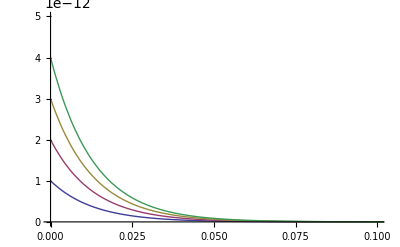

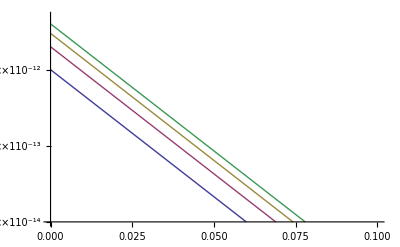

```mathematica
foo[a_,τtest_,t_]:=a*ⅇ^(-t/τtest);
a=100*10^-14;
τtest=0.013;
xMax=.1
Plot[{foo[a,τtest,t],foo[2 a,τtest,t],foo[3 a,τtest,t],foo[4 a,τtest,t]},{t,0,1.2},
PlotRange->{{0,xMax},{0,5 a}}]
LogPlot[{foo[a,τtest,t],foo[2 a,τtest,t],foo[3 a,τtest,t],foo[4 a,τtest,t]},{t,0,1.2},
PlotRange->{{0,xMax},{a/100,5 a}}]
```

#### Exponential with offset

0.05

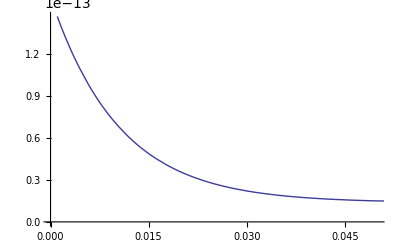

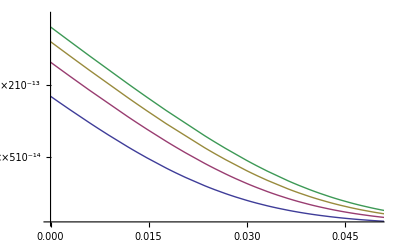

```mathematica
fooOff[a_,τtest_,t_,offset_]:=a*ⅇ^(-t/τtest)+offset;
atest=1.46548*10^-13;
τtest=0.0104876;
offsettest=1.36989*10^-14;
xMax=0.05
Plot[{fooOff[1 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{0,atest}}]
(*Plot[{fooOff[1 atest,τtest,t,offsettest],fooOff[2 atest,τtest,t,offsettest],fooOff[3 atest,τtest,t,offsettest],fooOff[4 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{0,5atest}}]*)
LogPlot[{fooOff[1 atest,τtest,t,offsettest],fooOff[2 atest,τtest,t,offsettest],fooOff[3 atest,τtest,t,offsettest],fooOff[4 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{atest/10,5atest}}]
```

### Random Commands that were once used

```mathematica
(*{Row[{Style["ylow:  ",FontFamily->"Helvetica", Bold] ,Style[boundedOffsetLessData⟦Position[boundedOffsetLessData,upperBound]⟦1,1⟧⟧⟦2⟧,Italic]}],
Row[{Style["yhigh:  ",FontFamily->"Helvetica", Bold] ,Style[boundedOffsetLessData⟦Position[boundedOffsetLessData,lowerBound]⟦1,1⟧⟧⟦2⟧,Italic]}]},*)
```

### Memory Analysis

```mathematica
MemoryInUse[]
```

45564400

```mathematica
(*DynamicModule[{pm={}},Dynamic@Refresh[pm=Append[pm,MemoryInUse[]];
If[Length[pm]>60,pm=Drop[pm,1]];
ListPlot[pm/1024/1024,AxesLabel->{"Time [s]","Memory [MB]"},PlotRange->Automatic],UpdateInterval->1,TrackedSymbols:>{}]]*)
Reverse@Sort[{ByteCount[Symbol[#]],#}&/@Names["`*"]]
```

### Slope Analysis

This section is to analyze how changing tau (by changing Ilk) should change the slope of y=-t/τ, where y is ln((I_sat-I_m)/(I_sat-I_o))in the actual simulation.  The first section uses a piecewise plot to visualize how increasing and lowering τ should change the slope of y.  The second section uses a Sin function to approximate what Ilk is doing in the actual simulation.  This analysis only applies to the rising edge; for the falling edge you would use a different equation for y.

```mathematica
y[t_,τ_]:=-t/τ;
```

#### Piecewise Analysis

```mathematica
padding={{25,5},{20,10}};
expRise[t_,Isat_,Io_,tc_,startx_]:=(Isat-Io)(1-ⅇ^((-(t-startx))/tc))+Io;
expDecay[t_,Isat_,Io_,tc_,startx_]:=(Isat-Io)ⅇ^((-(t-startx))/tc)+Io;
dampSine[t_,amp_,freq_,phase_,o_,tc_]:=amp*ⅇ^(-t/tc)*Sin[t/freq+phase]+o;
sine[t_,amp_,freq_,phase_,o_]:=amp*Sin[t/freq+phase]+o;
parab[t_,amp_,shift_,o_]:=amp*(t-shift)^2+o;
dur1=.2;dur2=.2;dur3=.2;dur4=.2;dur5=.2;
t1=dur1;
t2=dur1+dur2;
t3=dur1+dur2+dur3;
t4=dur1+dur2+dur3+dur4;
t5=dur1+dur2+dur3+dur4+dur5;
τ1=0.002;τ2=.005;τ3=0.010;τ4=.015;τ5=0.020;
(*maxX=Max[1.2,t5+.2];*)
imgSz=350;
Isat1=1/τ1; Io1=1/τ3;tc1=.09;
adS=-100; fdS=.035;pdS=0;odS=150;tcdS=.1;
aS=-100; fS=.03;pS=0;oS=150;tcS=.1;
aP=10000; sP=.15;oP=50;
Manipulate[
pw1=Piecewise[{
{expDecay[t,Isat1,Io1,tc1,0],0≤t<t1},
{expDecay[t1,Isat1,Io1,tc1,0],t1≤t<t2},
{1/τ2 (t-t2)+expDecay[t1,Isat1,Io1,tc1,0],t2≤t<t3},
{-1/τ3(t-t3)+1/τ2 (t3-t2)+expDecay[t1,Isat1,Io1,tc1,0],t3≤t<t4},
{-1/τ3(t4-t3)+(1/τ2 (t3-t2))+(expDecay[t1,Isat1,Io1,tc1,0]),t4≤t<t5},
{-1/τ2(t-t5)-1/τ3(t4-t3)+(1/τ2 (t3-t2))+(expDecay[t1,Isat1,Io1,tc1,0]),t5≤t<maxX}
},0.01];
pw2=Piecewise[{
{dampSine[t,adS,fdS,pdS,odS,tcdS],0≤t<t1},
{dampSine[t1,adS,fdS,pdS,odS,tcdS],t1≤t<t2},
{1/τ2 (t-t2)+dampSine[t1,adS,fdS,pdS,odS,tcdS],t2≤t<t3},
{-1/τ3(t-t3)+1/τ2 (t3-t2)+dampSine[t1,adS,fdS,pdS,odS,tcdS],t3≤t<t4},
{-1/τ3(t4-t3)+(1/τ2 (t3-t2))+(dampSine[t1,adS,fdS,pdS,odS,tcdS]),t4≤t<t5},
{-1/τ2(t-t5)-1/τ3(t4-t3)+(1/τ2 (t3-t2))+(dampSine[t1,adS,fdS,pdS,odS,tcdS]),t5≤t<maxX}
},0.01];
pw3=Piecewise[{
{sine[t,aS,fS,pS,oS],0≤t<t1},
{sine[t1,aS,fS,pS,oS],t1≤t<t2},
{1/τ2 (t-t2)+sine[t1,aS,fS,pS,oS],t2≤t<t3},
{-1/τ3(t-t3)+1/τ2 (t3-t2)+sine[t1,aS,fS,pS,oS],t3≤t<t4},
{-1/τ3(t4-t3)+(1/τ2 (t3-t2))+(sine[t1,aS,fS,pS,oS]),t4≤t<t5},
{-1/τ2(t-t5)-1/τ3(t4-t3)+(1/τ2 (t3-t2))+(sine[t1,aS,fS,pS,oS]),t5≤t<maxX}
},0.01];
pw4=Piecewise[{
{parab[t,aP,sP,oP],0≤t<t1},
{parab[t1,aP,sP,oP],t1≤t<t2},
{1/τ2 (t-t2)+parab[t1,aP,sP,oP],t2≤t<t3},
{-1/τ3(t-t3)+1/τ2 (t3-t2)+parab[t1,aP,sP,oP],t3≤t<t4},
{-1/τ3(t4-t3)+(1/τ2 (t3-t2))+(parab[t1,aP,sP,oP]),t4≤t<t5},
{-1/τ2(t-t5)-1/τ3(t4-t3)+(1/τ2 (t3-t2))+(parab[t1,aP,sP,oP]),t5≤t<maxX}
},0.01];
(*Row[{pw1,"\t",pw2, "\t",pw3}]*)
Grid[{
{Plot[{pw1,pw2,pw3,pw4},{t,0,maxX},PlotRange->{0,All},PlotLabel->"I_lk vs t", ImageSize->imgSz,ImagePadding->padding,PlotLegends->Placed[{"Exponent","Dampened Sine", "Sine","Parabola"},{0.75,0.75}]],
Plot[{1/pw1,1/pw2,1/pw3,1/pw4},{t,0,maxX},PlotRange->{0,All},PlotLabel->"τ vs t", ImageSize->imgSz,ImagePadding->padding]},
{Plot[{y[t,pw1],y[t,pw2],y[t,pw3],y[t,pw4]},{t,0,maxX},PlotRange->{All,0},PlotLabel->"y=-1/τt", ImageSize->imgSz,ImagePadding->padding],
Plot[{y[t,pw1],y[t,pw2],y[t,pw3],y[t,pw4]},{t,0,maxX},PlotRange->{All,0},PlotLabel->"y=-1/τt", ImageSize->imgSz,ImagePadding->padding]}
}],
{{maxX,t5},0.1,10,.1,Appearance->{"Labeled","Open"}}]
```

#### Sin Function Approximation Analysis

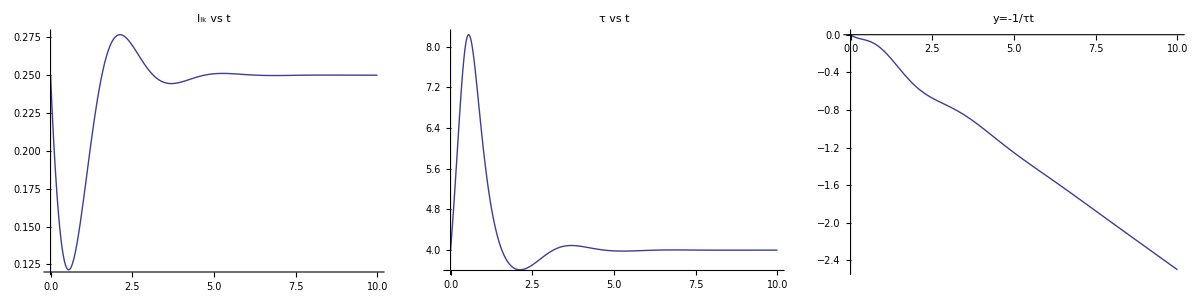

```mathematica
dampSine[t_,amp_,freq_,phase_,o_,tc_]:=amp*ⅇ^(-t/tc)*Sin[t/freq+phase]+o;
sine[t_,amp_,freq_,phase_,o_]:=amp*Sin[t/freq+phase]+o;
imgSzSin=350;
a=-.25;
f=.5;
p=0;
o=.25;
tcSin=1;
dsIlk=dampSine[t,a,f,p,o,tcSin];
sIlk=sine[t,a/2,f,p,o];
maxXSin=10;
Grid[{
{Plot[{dsIlk},{t,0,maxXSin},PlotRange->All,PlotLabel->"I_lk vs t", ImageSize->imgSzSin],
Plot[{1/dsIlk},{t,0,maxXSin},PlotRange->All,PlotLabel->"τ vs t", ImageSize->imgSzSin],
Plot[{y[t,1/dsIlk]},{t,0,maxXSin},PlotRange->{All,0},PlotLabel->"y=-1/τt", ImageSize->imgSzSin]}
}]
```